```mathematica
$Post=If[MatrixQ[#],MatrixForm[#],#]& (*Forces Display of Matrices*)
```

If[MatrixQ[#1],#1,#1]&

Joins two graph G1 and G2 along vertices in list L1 to vertices in L2

```mathematica
GJ[G1_,G2_,L1_,L2_]:=Module[{m,join},
m=VertexCount[G1];
join[{x_,y_}]:=x<->y;
joinedges[L_]:=Map[join,L];
edgemaker[L1,L2]:=MapThread[{#1,#2}&,{L1,L2}];
EdgeAdd[GraphDisjointUnion[G1,G2,VertexLabels->"Name"],joinedges[edgemaker[L1,L2]]]
];
```

Inputs Graph and makes directed paths from vertices in L1 to vertices in L2 respectively.

```mathematica
Handle[G1_,L1_,L2_]:=Module[{m,join,i},
m=VertexCount[G1];i=1;
join[{x_,y_}]:={x->(m+i),(m+i++)->y};
joinedges[L_]:=Map[join,L];
handlemaker[L1,L2]:=MapThread[{#1,#2}&,{L1,L2}];
EdgeAdd[Graph[G1,VertexLabels->"Name",GraphLayout->"SpringEmbedding",ImageSize->Tiny],Flatten[joinedges[handlemaker[L1,L2]],1]]
];
```

Finds determinant of a graph

```mathematica
GDet[G1_]:=Module[{},Det[AdjacencyMatrix[G1]]]
```

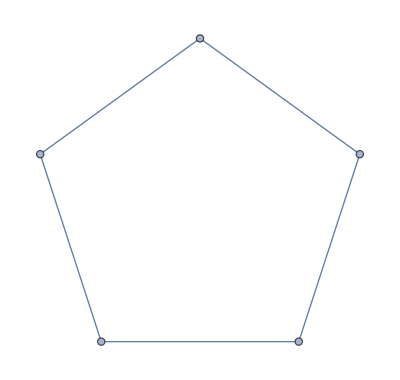
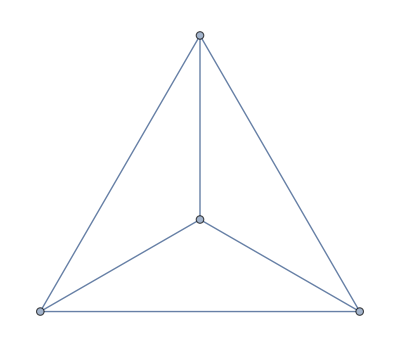

```mathematica
{CycleGraph[5], CompleteGraph[4]}
```

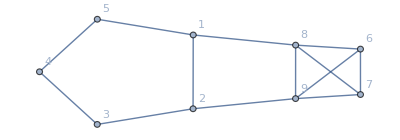

```mathematica
GJ[CycleGraph[5], CompleteGraph[4],{1,2},{8,9}]
GDet[%]
```

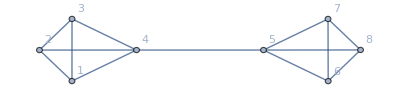

5

```mathematica
GJ[CompleteGraph[4], CompleteGraph[4], {4},{5}]
GDet[%]
```

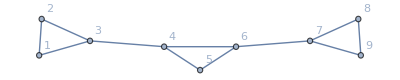

4

```mathematica
GJ[Test, CompleteGraph[3], {6},{7}]
GDet[%]
```

```mathematica
GDet[CompleteGraph[4]]
```

-3

```mathematica
Clear[m]
```

m=5

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[GraphicsBox[NamespaceBox[NetworkGraphics,DynamicModuleBox[{Typeset`graph=HoldComplete[«2211»]},TagBox[GraphicsGroupBox[{{«2»},{«21»}}],MouseAppearanceTag[NetworkGraphics]],AllowKernelInitialization→False]],{FormatType→TraditionalForm,«1»,DefaultBaseStyle→{N…cs,«1»}}]].

4

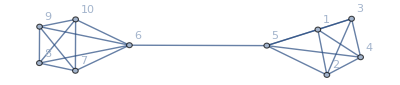

m=6

AdjacencyMatrix::graph: A graph object is expected at position 1 in AdjacencyMatrix[GraphicsBox[NamespaceBox[NetworkGraphics,DynamicModuleBox[{Typeset`graph=HoldComplete[«2211»]},TagBox[GraphicsGroupBox[{{«2»},{«21»}}],MouseAppearanceTag[NetworkGraphics]],AllowKernelInitialization→False]],{FormatType→TraditionalForm,«1»,DefaultBaseStyle→{N…cs,«1»}}]].

General::stop: Further output of AdjacencyMatrix::graph will be suppressed during this calculation.

-5

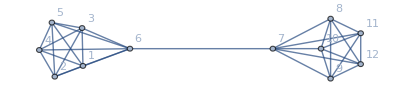

m=7

6

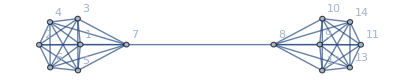

m=8

-7

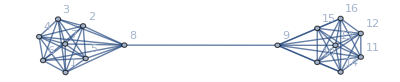

m=9

8

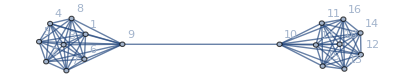

m=10

-9

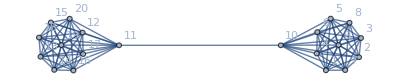

```mathematica
Do[
Print["m=",m];
Thing1 := GDet[CompleteGraph[m]];
Thing2:= GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}];
GDet[%];
Print[Thing1]; 
Print[Thing2],{m,5,10}]
```

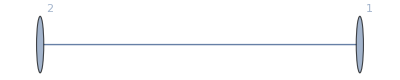
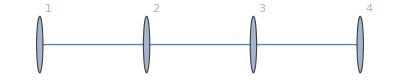
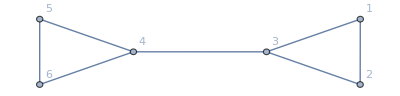
(1 | 0 | -Graphics- | -1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 3
4 | -3 | -Graphics- | 5)

```mathematica
Table[{m,
GDet[CompleteGraph[m]],
Thing1=GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],
GDet[Thing1]},{m,1,4}]
```

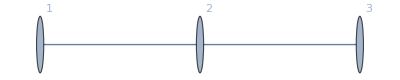
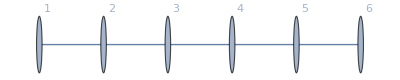
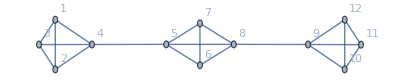
(1 | 0 | -Graphics- | 0
2 | -1 | -Graphics- | -1
3 | 2 | -Graphics- | 4
4 | -3 | -Graphics- | -7)

```mathematica
twoJoin=Table[{m,
GDet[CompleteGraph[m]],
Thing1=GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],
GDet[Thing1]},{m,1,4}]
```

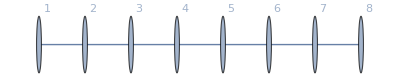
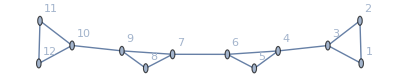
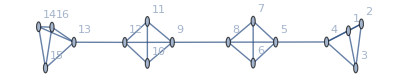
(1 | 0 | -Graphics- | 1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 5
4 | -3 | -Graphics- | 9)

```mathematica
threeJoin=Table[{m,
GDet[CompleteGraph[m]],
Thing1=GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],
GDet[Thing1]},{m,1,4}]
```

```mathematica
oneJoin=Table[{m,
GDet[CompleteGraph[m]],
Thing1=GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],
GDet[Thing1]},{m,1,4}]
```

(1 | 0 | -Graphics- | -1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 3
4 | -3 | -Graphics- | 5)

```mathematica
Grid[Prepend[oneJoin,{"m", "Determinant", "Joined Graph", "Determinant"}],Frame->All]
```

m | Determinant | Joined Graph | Determinant
1 | 0 | -Graphics- | -1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 3
4 | -3 | -Graphics- | 5

```mathematica
Grid[Prepend[oneJoin,{"m", "Determinant", "Joined Graph", "Determinant"}],Frame->All]
Grid[Prepend[twoJoin,{"m", "Determinant", "Joined Graph", "Determinant"}],Frame->All]
Grid[Prepend[threeJoin,{"m", "Determinant", "Joined Graph", "Determinant"}],Frame->All]
```

m | Determinant | Joined Graph | Determinant
1 | 0 | -Graphics- | -1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 3
4 | -3 | -Graphics- | 5

m | Determinant | Joined Graph | Determinant
1 | 0 | -Graphics- | 0
2 | -1 | -Graphics- | -1
3 | 2 | -Graphics- | 4
4 | -3 | -Graphics- | -7

m | Determinant | Joined Graph | Determinant
1 | 0 | -Graphics- | 1
2 | -1 | -Graphics- | 1
3 | 2 | -Graphics- | 5
4 | -3 | -Graphics- | 9

```mathematica
Table[{m,
GDet[CompleteGraph[m]],
Thing1=GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],
GDet[Thing1]},{m,1,4}]
```

```mathematica
allJoins=Table[{m,
GDet[CompleteGraph[m]],
GDet[GJ[CompleteGraph[m],CompleteGraph[m],{m},{m+1}]],GDet[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}]],
GDet[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}]],
GDet[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}]],
GDet[GJ[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}],CompleteGraph[m],{5m},{5m+1}]]
},{m,1,10}]
```

(1 | 0 | -1 | 0 | 1 | 0 | -1
2 | -1 | 1 | -1 | 1 | -1 | 1
3 | 2 | 3 | 4 | 5 | 6 | 7
4 | -3 | 5 | -7 | 9 | -11 | 13
5 | 4 | 7 | 10 | 13 | 16 | 19
6 | -5 | 9 | -13 | 17 | -21 | 25
7 | 6 | 11 | 16 | 21 | 26 | 31
8 | -7 | 13 | -19 | 25 | -31 | 37
9 | 8 | 15 | 22 | 29 | 36 | 43
10 | -9 | 17 | -25 | 33 | -41 | 49)

```mathematica
Grid[Prepend[allJoins,Style[#,{Black,Bold,14}]&/@{"m", "0-join", "1-join", "2-join", "3-join","4-join","5-join"}],Frame->All]
```

m | 0-join | 1-join | 2-join | 3-join | 4-join | 5-join
1 | 0 | -1 | 0 | 1 | 0 | -1
2 | -1 | 1 | -1 | 1 | -1 | 1
3 | 2 | 3 | 4 | 5 | 6 | 7
4 | -3 | 5 | -7 | 9 | -11 | 13
5 | 4 | 7 | 10 | 13 | 16 | 19
6 | -5 | 9 | -13 | 17 | -21 | 25
7 | 6 | 11 | 16 | 21 | 26 | 31
8 | -7 | 13 | -19 | 25 | -31 | 37
9 | 8 | 15 | 22 | 29 | 36 | 43
10 | -9 | 17 | -25 | 33 | -41 | 49

```mathematica
allJoinsMin=Table[{m,
GDet[CompleteGraph[m]],
GDet[GJ[CompleteGraph[m],CompleteGraph[m],{m},{m+1}]],GDet[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}]],
GDet[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}]],
GDet[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}]],
GDet[GJ[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}],CompleteGraph[m],{5m},{5m+1}]]
},{m,3,10}]

Grid[Prepend[allJoinsMin,Style[#,{Black,Bold,14}]&/@{"m", "0-join", "1-join", "2-join", "3-join","4-join","5-join"}],Frame->All]
```

(3 | 2 | 3 | 4 | 5 | 6 | 7
4 | -3 | 5 | -7 | 9 | -11 | 13
5 | 4 | 7 | 10 | 13 | 16 | 19
6 | -5 | 9 | -13 | 17 | -21 | 25
7 | 6 | 11 | 16 | 21 | 26 | 31
8 | -7 | 13 | -19 | 25 | -31 | 37
9 | 8 | 15 | 22 | 29 | 36 | 43
10 | -9 | 17 | -25 | 33 | -41 | 49)

m | 0-join | 1-join | 2-join | 3-join | 4-join | 5-join
3 | 2 | 3 | 4 | 5 | 6 | 7
4 | -3 | 5 | -7 | 9 | -11 | 13
5 | 4 | 7 | 10 | 13 | 16 | 19
6 | -5 | 9 | -13 | 17 | -21 | 25
7 | 6 | 11 | 16 | 21 | 26 | 31
8 | -7 | 13 | -19 | 25 | -31 | 37
9 | 8 | 15 | 22 | 29 | 36 | 43
10 | -9 | 17 | -25 | 33 | -41 | 49

```mathematica
FindSequenceFunction[{{0,3},{1,5},{2,7},{3,9},{4,11},{5,13}}]
```

1+2 (1+#1)&

```mathematica
FindSequenceFunction[{{0,4},{1,7},{2,10},{3,13},{4,16},{5,19}}]
```

1+3 (1+#1)&

```mathematica
FindSequenceFunction[{{0,5},{1,9},{2,13},{3,17},{4,21},{5,25}}]
```

1+4 (1+#1)&

```mathematica
allJoinsMinCycle=Table[{m,
GDet[CycleGraph[m]],
GDet[GJ[CycleGraph[m],CycleGraph[m],{m},{m+1}]],GDet[GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2m},{2m+1}]],
GDet[GJ[GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2m},{2m+1}],CycleGraph[m],{3m},{3m+1}]],
GDet[GJ[GJ[GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2m},{2m+1}],CycleGraph[m],{3m},{3m+1}],CycleGraph[m],{4m},{4m+1}]],
GDet[GJ[GJ[GJ[GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2m},{2m+1}],CycleGraph[m],{3m},{3m+1}],CycleGraph[m],{4m},{4m+1}],CycleGraph[m],{5m},{5m+1}]]
},{m,1,10}]
```

(1 | 1 | 0 | -1 | -1 | 0 | 1
2 | -4 | 16 | -64 | 256 | -1024 | 4096
3 | 2 | 3 | 4 | 5 | 6 | 7
4 | 0 | 0 | 0 | 0 | 0 | 0
5 | 2 | 3 | 4 | 5 | 6 | 7
6 | -4 | 16 | -64 | 256 | -1024 | 4096
7 | 2 | 3 | 4 | 5 | 6 | 7
8 | 0 | 0 | 0 | 0 | 0 | 0
9 | 2 | 3 | 4 | 5 | 6 | 7
10 | -4 | 16 | -64 | 256 | -1024 | 4096)

4

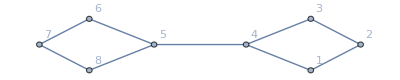

0

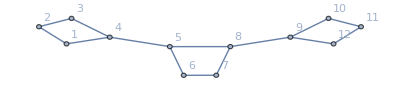

0

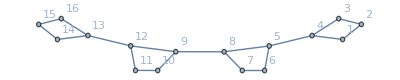

0

```mathematica
m=4
GJ[CycleGraph[m],CycleGraph[m],{m},{m+1}]
GDet[%]
GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2*m},{2*m+1}]
GDet[%]
GJ[GJ[GJ[CycleGraph[m], CycleGraph[m], {m},{m+1}],CycleGraph[m],{2m},{2m+1}],CycleGraph[m],{3m},{3m+1}]
GDet[%]
```

```mathematica
Grid[Prepend[allJoinsMinCycle,Style[#,{Black,Bold,14}]&/@{"m", "0-join", "1-join", "2-join", "3-join","4-join","5-join"}],Frame->All]
```

m | 0-join | 1-join | 2-join | 3-join | 4-join | 5-join
1 | 1 | 0 | -1 | -1 | 0 | 1
2 | -4 | 16 | -64 | 256 | -1024 | 4096
3 | 2 | 3 | 4 | 5 | 6 | 7
4 | 0 | 0 | 0 | 0 | 0 | 0
5 | 2 | 3 | 4 | 5 | 6 | 7
6 | -4 | 16 | -64 | 256 | -1024 | 4096
7 | 2 | 3 | 4 | 5 | 6 | 7
8 | 0 | 0 | 0 | 0 | 0 | 0
9 | 2 | 3 | 4 | 5 | 6 | 7
10 | -4 | 16 | -64 | 256 | -1024 | 4096

```mathematica
allJoinsMin=Table[{m,
GDet[CompleteGraph[m]],
GDet[GJ[CompleteGraph[m],CompleteGraph[m],{m},{m+1}]],GDet[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}]],
GDet[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}]],
GDet[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}]],
GDet[GJ[GJ[GJ[GJ[GJ[CompleteGraph[m], CompleteGraph[m], {m},{m+1}],CompleteGraph[m],{2m},{2m+1}],CompleteGraph[m],{3m},{3m+1}],CompleteGraph[m],{4m},{4m+1}],CompleteGraph[m],{5m},{5m+1}]]
},{m,3,10}]
```